## MPO Tensors

### Square Lattice (FPL)

#### Vertex Tensor (FPL)

Starting from the vertex tensor for FPL (for β=0 only)

X[σ_i]=δ(σ_1 σ_2+σ_2 σ_3+σ_3 σ_4+σ_4 σ_1) ⅇ^(ⅈ θ (σ_1+σ_2+σ_3+σ_4)/8),

with the angle θ parameterize the θ-term. σ_i=±1, and the labeling convesion as follows.

```mathematica
Null
```

-Graphics-

δ term make sure the edges are two-occupied-two-empty by the domain wall (σ_i σ_(i+1)=±1 for domain wall empty/occupation, so they must add to to 0). On the exponent, if ∑σ=0, spins are balanced, domain wall is straight, otherwise more up → positive angle, more down → negative angle.

Tensor code: Q=ⅈ θ

```mathematica
Module[{X},
X=Table[KroneckerDelta[σ1 σ2+σ2 σ3+σ3 σ4+σ4 σ1]EXP[Q((σ1+σ2+σ3+σ4)/8)],{σ1,{1,-1}},{σ2,{1,-1}},{σ3,{1,-1}},{σ4,{1,-1}}];
CellPrint@Cell[TensorCode[SparseArray[X],PostRules->{"EXP(0)"->"Z1"}],"Program"]]
```

TENSOR([2,2,2,2],[1,2,3,4,6,7,8,9,11,12,13,14],[EXP(Q/4.),EXP(Q/4.),Z1,EXP(Q/4.),Z1,EXP(-Q/4.),EXP(Q/4.),Z1,EXP(-Q/4.),Z1,EXP(-Q/4.),EXP(-Q/4.)])

#### Make MPO

```mathematica
Null
```

Null

Null

Null

```mathematica
Null
```

Null

Null

```mathematica
Null
```

Null

Null

Null

```mathematica
Null
```

Null

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

#### Initialization

```mathematica
Null
```

Null

#### System Tensor

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

### Square Lattice (Loop Gas)

#### Vertex Tensor (LG)

Starting from the vertex tensor for O(n) model (loop gas)

X[σ_i]=ⅇ^(ⅈ θ (σ_1+σ_3-σ_1 σ_3(σ_2+σ_4))/8)ⅇ^(β(σ_1 σ_2+σ_2 σ_3+σ_3 σ_4+σ_4 σ_1)/2),

with the angle θ parameterize the θ-term, and β is the string tension. σ_i=±1, and the labeling convesion as follows.

```mathematica
Null
```

-Graphics-

The strings are not intersecting. The ansatz is 𝒯-rev symmetric but breaks the C_4 rotational symmetry.

```mathematica
Module[{X},
X=Table[EXP[Q((σ1+σ3-σ1 σ3(σ2+σ4))/8)+B((σ1 σ2+σ2 σ3+σ3 σ4+σ4 σ1)/2)],{σ1,{1,-1}},{σ2,{1,-1}},{σ3,{1,-1}},{σ4,{1,-1}}];
CellPrint@Cell[TensorCode[SparseArray[X],PostRules->{"0"->"Z0","1"->"Z1"}],"Program"]]
```

Null

#### Make MPO

```mathematica
Null
```

Null

Null

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

#### Test MPO

```mathematica
Null
```

Null

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

#### System Tensor

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

#### Measurement

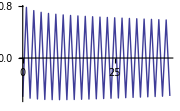
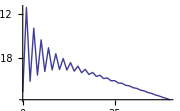
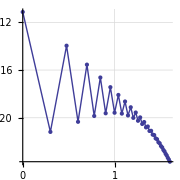

```mathematica
Module[{M0,M1,M2,val,vec,data},
{M0,M1,M2}=TensorLoad/@{"M0","M1","M2"};
{val,vec}=First@Thread@Eigensystem@M0;
M0=M0/val;
M1=M1/val;
M2=M2/val;
data=Table[{x,Chop[Conjugate[vec].M1.MatrixPower[M0,x].M2.vec]},{x,0,40}];
Print@{ListLinePlot[data,PlotRange->All,ImageSize->180],ListLinePlot[{#1,Log[10,Abs[#2]]}&@@@data,PlotRange->All,ImageSize->180],
ListLinePlot[{Log[10,#1],Log[10,Abs[#2]]}&@@@data,GridLines->{Range[0,5,0.1],Range[-10,0,0.1]},PlotRange->All,Mesh->Full,AspectRatio->Automatic,ImageSize->180]}
]
```

#### Solver

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

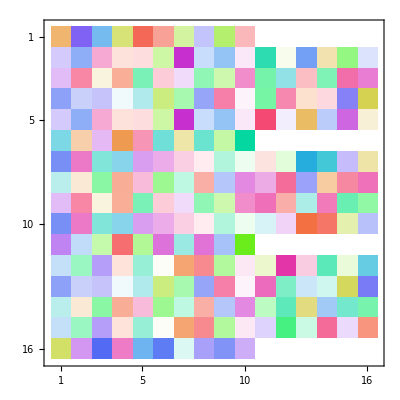
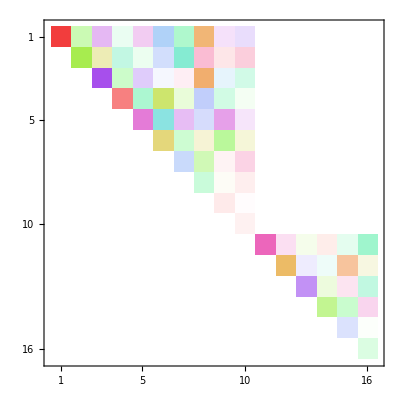

```mathematica
Null
```

### Square Lattice (Loop Gas, Avoid Crossing)

#### Vertex Tensor (LG)

Starting from the vertex tensor for O(n) model (loop gas)

X[σ_i]=ⅇ^(ⅈ θ (σ_1+σ_3-σ_1 σ_3(σ_2+σ_4))/8)ⅇ^(β(σ_1 σ_2+σ_2 σ_3+σ_3 σ_4+σ_4 σ_1)/2)1/8((7+K)+(1-K)(σ_1 σ_2+σ_2 σ_3+σ_3 σ_4+σ_4 σ_1-σ_1 σ_3-σ_2 σ_4-σ_1 σ_2 σ_3 σ_4)),

with the angle θ parameterize the θ-term, and β is the string tension. σ_i=±1, and the labeling convesion as follows.

```mathematica
Null
```

-Graphics-

The strings are not intersecting. The ansatz is 𝒯-rev symmetric but breaks the C_4 rotational symmetry.

```mathematica
Module[{X},
X=Table[EXP[Q((σ1+σ3-σ1 σ3(σ2+σ4))/8)+B((σ1 σ2+σ2 σ3+σ3 σ4+σ4 σ1)/2)]If[MatchQ[{{σ1,σ2},{σ4,σ3}},{{a_,b_},{b_,a_}}/;a==-b],CROSS,1],{σ1,{1,-1}},{σ2,{1,-1}},{σ3,{1,-1}},{σ4,{1,-1}}];
CellPrint@Cell[TensorCode[SparseArray[X],PostRules->{"0"->"Z0","1"->"Z1"}],"Program"]]
```

TENSOR([2,2,2,2],[0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15],[EXP(2*B),EXP(Q/4.),EXP(Q/4.),EXP(Z0),EXP(Q/4.),CROSS*EXP(-2*B - Q/2.),EXP(Z0),EXP(-Q/4.),EXP(Q/4.),EXP(Z0),CROSS*EXP(-2*B + Q/2.),EXP(-Q/4.),EXP(Z0),EXP(-Q/4.),EXP(-Q/4.),EXP(2*B)])

```mathematica
Module[{X},
X=Table[EXP[Q((σ1+σ3-σ1 σ3(σ2+σ4))/8)+B((σ1 σ2+σ2 σ3+σ3 σ4+σ4 σ1)/2)],{σ1,{1,-1}},{σ2,{1,-1}},{σ3,{1,-1}},{σ4,{1,-1}}];
CellPrint@Cell[TensorCode[SparseArray[X],PostRules->{"0"->"Z0","1"->"Z1"}],"Program"]]
```

TENSOR([2,2,2,2],[0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15],[EXP(2*B),EXP(Q/4.),EXP(Q/4.),EXP(Z0),EXP(Q/4.),EXP(-2*B - Q/2.),EXP(Z0),EXP(-Q/4.),EXP(Q/4.),EXP(Z0),EXP(-2*B + Q/2.),EXP(-Q/4.),EXP(Z0),EXP(-Q/4.),EXP(-Q/4.),EXP(2*B)])

```mathematica
Module[{ops,F,W},
ops=σ@@@Tuples[{0,3},4];
F=Normal[Diagonal/@Represent/@ops];
W=Flatten@Table[If[MatchQ[{{σ1,σ2},{σ4,σ3}},{{a_,b_},{b_,a_}}/;a==-b],K,1],{σ1,{1,-1}},{σ2,{1,-1}},{σ3,{1,-1}},{σ4,{1,-1}}];
Simplify[ops.F.W]]
```

2 ((7+K) σ[0,0,0,0]-(-1+K) (σ[0,0,3,3]-σ[0,3,0,3]+σ[0,3,3,0]+σ[3,0,0,3]-σ[3,0,3,0]+σ[3,3,0,0]-σ[3,3,3,3]))

## Test

#### Correlation

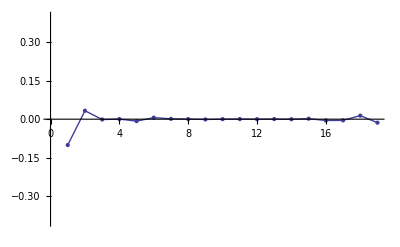

```mathematica
ListLinePlot[Most@Chop@FortranGet["C"],Mesh->All,PlotRange->{-0.4,0.4}]
```

{A→0.343054,α→1.1852,k→1.51059,ϕ→-1.47855}

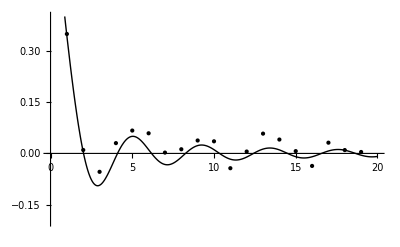

```mathematica
Module[{data,model,fit},
data=MapIndexed[{First[#2],#1}&,Rest@Reverse@Chop@FortranGet["C"]];
model=A x^(-α)Cos[k x+ϕ];
fit=FindFit[data,model,{{A,0.3},{α,2},{k,2π/4},{ϕ,0}},x];
Print[fit];
Plot[model/.fit,{x,0,20},PlotStyle->Black,PlotRange->{-0.2,0.4},Epilog->{PointSize[Absolute[4]],Map[Point,data]}]]
```

{A→-0.100722,α→57.0157,k→0.,ϕ→0.}

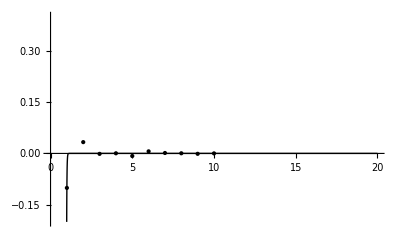

```mathematica
Module[{data,model,fit},
data=MapIndexed[{First[#2],#1}&,Chop@FortranGet["C"]⟦1;;10⟧];
model=A x^(-α)Cos[k x+ϕ];
fit=FindFit[data,model,{{A,0.2},{α,2},{k,0.},{ϕ,0}},x];
Print[fit];
Plot[model/.fit,{x,0,20},PlotStyle->Black,PlotRange->{-0.2,0.4},Epilog->{PointSize[Absolute[4]],Map[Point,data]}]]
```

```mathematica
FortranGet["A"]//Eigenvalues
```

{473.472+5.80036×10^-17 ⅈ,461.443+5.05447×10^-18 ⅈ,168.582-1.2517×10^-17 ⅈ,149.115+1.02341×10^-16 ⅈ,126.621+5.23689×10^-17 ⅈ,82.9563-4.82582×10^-17 ⅈ,78.8287-1.49735×10^-17 ⅈ,77.1139+6.05203×10^-18 ⅈ,75.5772-6.18525×10^-17 ⅈ,74.6498+5.50039×10^-18 ⅈ,74.6498+2.1774×10^-18 ⅈ,56.4392-8.898×10^-17 ⅈ,50.6951+7.86818×10^-17 ⅈ,48.8309+1.95512×10^-16 ⅈ,48.4053+3.28859×10^-17 ⅈ,42.9599+9.68346×10^-18 ⅈ,42.6253+6.27422×10^-17 ⅈ,39.7884+5.89806×10^-17 ⅈ,39.7884+1.65043×10^-16 ⅈ,37.6981+3.46733×10^-17 ⅈ,36.7539-4.75205×10^-18 ⅈ,33.2786+2.3505×10^-17 ⅈ,30.4114-3.78382×10^-16 ⅈ,25.718+7.16328×10^-17 ⅈ,22.7331+3.62033×10^-17 ⅈ,22.1207-4.81658×10^-17 ⅈ,20.6342-3.78929×10^-17 ⅈ,20.6342-3.67761×10^-16 ⅈ,19.9083+8.80045×10^-17 ⅈ,16.2659-1.25554×10^-17 ⅈ,13.5319+1.26265×10^-17 ⅈ,13.4963+7.91117×10^-17 ⅈ,12.8176+2.65208×10^-17 ⅈ,12.8128-7.08698×10^-18 ⅈ,9.96449+6.5301×10^-16 ⅈ,8.29019+8.14008×10^-17 ⅈ,7.85497-3.94763×10^-18 ⅈ,7.52342+2.58054×10^-17 ⅈ,7.12973+2.19194×10^-16 ⅈ,7.12973+4.98438×10^-17 ⅈ,6.30224+6.37197×10^-20 ⅈ,5.21328+3.59489×10^-17 ⅈ,4.52053-3.80891×10^-17 ⅈ,4.36664+1.37153×10^-17 ⅈ,4.29945-5.58143×10^-17 ⅈ,4.07357-1.79571×10^-17 ⅈ,3.87677+1.67176×10^-17 ⅈ,3.77284+1.08362×10^-16 ⅈ,3.63429+2.21734×10^-17 ⅈ,3.34841+1.11022×10^-15 ⅈ,3.34841-1.21778×10^-15 ⅈ,2.87178+6.44157×10^-18 ⅈ,2.55292+7.54126×10^-17 ⅈ,2.53081+8.3299×10^-18 ⅈ,2.17122-1.09077×10^-17 ⅈ,2.06255-2.35197×10^-17 ⅈ,1.95381+2.13718×10^-15 ⅈ,1.95381-1.9984×10^-15 ⅈ,1.84829+2.51249×10^-16 ⅈ,1.65396+6.18115×10^-18 ⅈ,1.08695+2.16595×10^-17 ⅈ,1.07732-4.35057×10^-18 ⅈ,0.353286+8.83976×10^-17 ⅈ,0.351607+2.24472×10^-17 ⅈ}

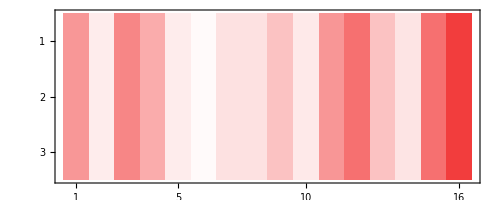

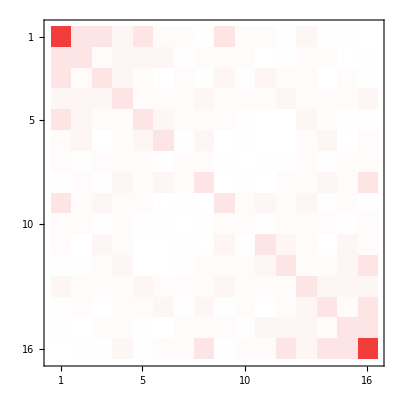
{-Graphics-,-Graphics-}

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

```mathematica
Module[{A,W0,WA,WB,l,r,Ts},
{A,W0,WA,WB,l,r,Ts}=FortranGet/@{"A","W0","WA","WB","LINDS","RINDS","TS"};
Print@ComplexMatrixPlot@{A.W0,WA,WB};
Print[ComplexMatrixPlot/@{A,SparseArray[{#1+1,#2+1}->#3&@@@Thread@{l,r,Ts}]}];
A-SparseArray[{#1+1,#2+1}->#3&@@@Thread@{l,r,Ts}]
]
```

#### Correlation

```mathematica
TensorLoad["M"]//Chop//MatrixForm
```

(0 | 0.121202 | 0.00502907 | 0.0088192 | 0.0257783 | 0.00656894 | -0.016798 | 0.000445434 | 0.0203086 | 0.0176966 | 0.0330456 | 0.270312
0 | 0 | 0.135705 | 0.0226368 | 0.01319 | 0.0178268 | -0.00924208 | -0.0150227 | -0.00521249 | 0.0106668 | 0.0153732 | 0.0258192
0 | 0 | 0 | 0.130308 | 0.01319 | 0.0144296 | 0.00849466 | -0.0059212 | -0.0123088 | -0.00337262 | 0.00657132 | 0.00232762
0 | 0 | 0 | 0 | 0.140788 | 0.0313699 | 0.0138319 | 0.0106848 | -0.00326121 | -0.011148 | -0.000813543 | 0.0385378
0 | 0 | 0 | 0 | 0 | 0.132176 | 0.0201834 | 0.0158866 | 0.0105897 | -0.00282986 | -0.00675698 | 0.0276946
0 | 0 | 0 | 0 | 0 | 0 | 0.126715 | 0.016129 | 0.00764518 | 0.0100954 | -0.000277466 | -0.003983
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.137119 | 0.0179886 | 0.00904855 | 0.0019584 | -0.0118147
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.136656 | 0.0187372 | -0.00411729 | 0.0165848
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.138524 | 0.0208943 | 0.0158102
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.142669 | 0.0586944
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.304238
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ListPlot3D[TensorLoad["M"]//Chop,PlotRange->All]
```

-Graphics3D-

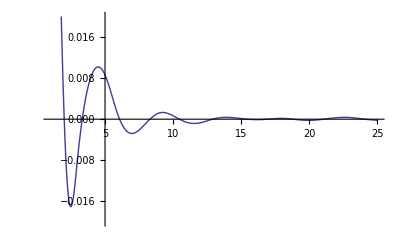

```mathematica
Module[{M,L},
M=TensorLoad["M"];
L=Length[M];
ListLinePlot[Chop@Mean[Join[Diagonal[M,#],Diagonal[M,L-#]]]&/@Range[L/2],PlotRange->{-0.02,0.02},InterpolationOrder->3]]
```

{30,0.0513014}

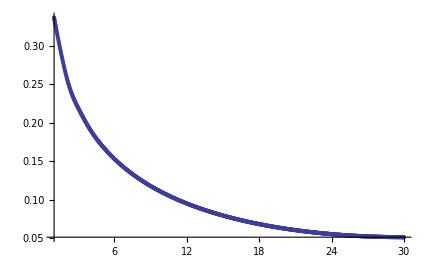

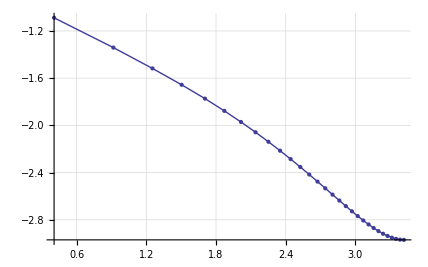

```mathematica
Module[{M,L,data},
M=TensorLoad["M"];
L=Length[M];
data=MapIndexed[{First[#2],#1}&,Re@Mean[Join[Diagonal[M,#],Diagonal[M,L-#]]]&/@Range[L/2]];
Print[Last[data]];
Print@ListLinePlot[data,PlotRange->All,InterpolationOrder->3,Mesh->All];
ListLinePlot[{Log[#1+0.5],Log[#2]}&@@@data,GridLines->{Range[0,4,0.1],Range[-20,7,0.1]},AspectRatio->Automatic,PlotRange->All,InterpolationOrder->1,Mesh->All]]
```

#### Correlation

```mathematica
TensorLoad["M"]//Chop//MatrixForm
```

(0 | 0.325777 | 0.253047 | 0.212254 | 0.184791 | 0.164319 | 0.14814 | 0.134883 | 0.123751 | 0.114243 | 0.10602 | 0.0988428 | 0.0925332 | 0.0869572 | 0.0820126 | 0.0776159 | 0.0737028 | 0.0702199 | 0.0671222 | 0.0643744 | 0.0619464 | 0.059813 | 0.0579528 | 0.0563481 | 0.0549846 | 0.0538508 | 0.0529348 | 0.0522307 | 0.0517316 | 0.0514342 | 0.051336 | 0.0514358 | 0.0517351 | 0.0522356 | 0.052941 | 0.0538576 | 0.0549929 | 0.0563564 | 0.05796 | 0.059819 | 0.0619504 | 0.0643747 | 0.0671183 | 0.0702102 | 0.0736873 | 0.0775924 | 0.0819798 | 0.0869145 | 0.0924778 | 0.0987734 | 0.105935 | 0.114138 | 0.123625 | 0.134735 | 0.147971 | 0.164135 | 0.184603 | 0.212084 | 0.252908 | 0.650816
0 | 0 | 0.325784 | 0.253074 | 0.212288 | 0.184823 | 0.164345 | 0.148158 | 0.134893 | 0.123754 | 0.114242 | 0.106016 | 0.098836 | 0.092525 | 0.0869493 | 0.082006 | 0.0776137 | 0.0737064 | 0.0702307 | 0.0671434 | 0.0644084 | 0.061995 | 0.0598778 | 0.0580358 | 0.0564513 | 0.0551105 | 0.0539995 | 0.0531093 | 0.0524324 | 0.051962 | 0.051695 | 0.0516278 | 0.0517599 | 0.0520923 | 0.0526264 | 0.053367 | 0.0543188 | 0.0554896 | 0.0568887 | 0.0585281 | 0.0604218 | 0.0625863 | 0.0650424 | 0.0678143 | 0.0709308 | 0.0744266 | 0.0783435 | 0.082732 | 0.0876533 | 0.0931861 | 0.0994259 | 0.106498 | 0.114566 | 0.123856 | 0.134683 | 0.147525 | 0.163158 | 0.183003 | 0.210145 | 0.50584
0 | 0 | 0 | 0.325802 | 0.253097 | 0.212309 | 0.184847 | 0.164365 | 0.148173 | 0.134902 | 0.12376 | 0.114243 | 0.106011 | 0.0988248 | 0.0925057 | 0.0869214 | 0.0819682 | 0.0775643 | 0.0736442 | 0.0701555 | 0.0670545 | 0.0643046 | 0.0618755 | 0.0597424 | 0.0578842 | 0.0562837 | 0.0549254 | 0.0537975 | 0.0528905 | 0.0521957 | 0.051708 | 0.0514226 | 0.0513368 | 0.0514504 | 0.0517633 | 0.0522783 | 0.0529986 | 0.0539298 | 0.0550795 | 0.056457 | 0.0580745 | 0.0599448 | 0.0620862 | 0.0645183 | 0.0672654 | 0.070357 | 0.0738273 | 0.0777179 | 0.0820799 | 0.086976 | 0.0924827 | 0.0986979 | 0.105748 | 0.113799 | 0.123079 | 0.133914 | 0.146807 | 0.162608 | 0.182999 | 0.424205
0 | 0 | 0 | 0 | 0.325809 | 0.253105 | 0.212313 | 0.184857 | 0.164377 | 0.148181 | 0.134904 | 0.123754 | 0.114231 | 0.105992 | 0.0987959 | 0.0924671 | 0.0868711 | 0.0819039 | 0.0774845 | 0.0735476 | 0.0700405 | 0.0669192 | 0.0641475 | 0.061696 | 0.0595392 | 0.0576572 | 0.056031 | 0.0546468 | 0.0534925 | 0.052558 | 0.0518358 | 0.0513198 | 0.0510055 | 0.0508908 | 0.0509748 | 0.0512581 | 0.0517426 | 0.0524324 | 0.0533331 | 0.0544521 | 0.0557995 | 0.0573861 | 0.0592271 | 0.0613398 | 0.0637441 | 0.066466 | 0.0695347 | 0.0729856 | 0.076862 | 0.0812176 | 0.0861152 | 0.0916364 | 0.0978832 | 0.104989 | 0.113128 | 0.122542 | 0.133584 | 0.146801 | 0.163148 | 0.369241
0 | 0 | 0 | 0 | 0 | 0.325812 | 0.253107 | 0.212307 | 0.18486 | 0.164385 | 0.148186 | 0.134901 | 0.123744 | 0.114211 | 0.105962 | 0.0987563 | 0.0924167 | 0.0868081 | 0.0818271 | 0.0773921 | 0.0734384 | 0.0699123 | 0.0667706 | 0.0639775 | 0.061503 | 0.0593231 | 0.0574157 | 0.0557641 | 0.0543537 | 0.0531724 | 0.0522104 | 0.0514602 | 0.0509156 | 0.0505728 | 0.0504294 | 0.0504844 | 0.0507386 | 0.051194 | 0.0518552 | 0.0527276 | 0.0538195 | 0.0551397 | 0.0567012 | 0.0585191 | 0.0606105 | 0.0629973 | 0.0657059 | 0.0687665 | 0.072217 | 0.0761034 | 0.0804796 | 0.0854155 | 0.0909963 | 0.0973327 | 0.104564 | 0.11288 | 0.122539 | 0.133904 | 0.147511 | 0.328301
0 | 0 | 0 | 0 | 0 | 0 | 0.325813 | 0.253108 | 0.212296 | 0.18486 | 0.16439 | 0.148189 | 0.134897 | 0.123729 | 0.114185 | 0.105926 | 0.0987107 | 0.0923594 | 0.0867388 | 0.0817447 | 0.0772956 | 0.0733259 | 0.0697825 | 0.0666222 | 0.0638091 | 0.0613143 | 0.0591122 | 0.0571823 | 0.0555076 | 0.0540732 | 0.0528673 | 0.0518806 | 0.051105 | 0.0505352 | 0.0501671 | 0.0499984 | 0.0500282 | 0.0502575 | 0.0506889 | 0.0513266 | 0.0521771 | 0.0532475 | 0.0545489 | 0.056094 | 0.0578983 | 0.05998 | 0.0623631 | 0.0650734 | 0.0681446 | 0.0716169 | 0.0755375 | 0.0799666 | 0.0849779 | 0.0906648 | 0.0971429 | 0.104564 | 0.113124 | 0.123068 | 0.134669 | 0.295971
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325813 | 0.253108 | 0.212283 | 0.184856 | 0.164394 | 0.14819 | 0.13489 | 0.123712 | 0.114157 | 0.105888 | 0.0986609 | 0.0922988 | 0.0866667 | 0.0816607 | 0.0771985 | 0.0732143 | 0.0696554 | 0.0664787 | 0.0636488 | 0.0611355 | 0.0589142 | 0.0569649 | 0.0552697 | 0.0538144 | 0.0525875 | 0.0515793 | 0.0507823 | 0.0501911 | 0.0498019 | 0.0496123 | 0.0496218 | 0.0498316 | 0.0502444 | 0.0508654 | 0.0517 | 0.0527574 | 0.0540487 | 0.0555868 | 0.0573882 | 0.0594737 | 0.0618661 | 0.0645953 | 0.0676969 | 0.0712122 | 0.0751946 | 0.0797081 | 0.0848329 | 0.0906668 | 0.0973345 | 0.104987 | 0.113792 | 0.123843 | 0.269492
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325813 | 0.253108 | 0.212267 | 0.18485 | 0.164395 | 0.148191 | 0.134883 | 0.123694 | 0.114128 | 0.105847 | 0.0986095 | 0.092237 | 0.0865943 | 0.081577 | 0.0771027 | 0.0731059 | 0.0695339 | 0.0663433 | 0.0634983 | 0.0609692 | 0.058732 | 0.0567656 | 0.0550531 | 0.0535803 | 0.0523356 | 0.0513095 | 0.0504949 | 0.0498866 | 0.0494804 | 0.0492746 | 0.0492689 | 0.0494645 | 0.0498652 | 0.0504751 | 0.0513015 | 0.0523539 | 0.0536432 | 0.0551842 | 0.0569949 | 0.0590958 | 0.061513 | 0.0642783 | 0.0674288 | 0.0710114 | 0.0750825 | 0.0797122 | 0.0849845 | 0.0910027 | 0.0978867 | 0.105745 | 0.114557 | 0.247269
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325813 | 0.253108 | 0.21225 | 0.184842 | 0.164395 | 0.148189 | 0.134875 | 0.123676 | 0.114098 | 0.105806 | 0.0985582 | 0.0921755 | 0.0865227 | 0.081495 | 0.0770103 | 0.0730025 | 0.0694192 | 0.0662164 | 0.0633586 | 0.0608167 | 0.0585656 | 0.0565852 | 0.0548583 | 0.0533711 | 0.0521117 | 0.0510715 | 0.0502432 | 0.0496213 | 0.0492024 | 0.048985 | 0.0489688 | 0.0491561 | 0.0495495 | 0.0501552 | 0.0509806 | 0.0520353 | 0.0533319 | 0.0548864 | 0.0567168 | 0.0588465 | 0.0613038 | 0.0641219 | 0.0673423 | 0.0710155 | 0.0752031 | 0.0799776 | 0.0854267 | 0.091645 | 0.0987004 | 0.106493 | 0.228291
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325812 | 0.253107 | 0.212232 | 0.184832 | 0.164392 | 0.148187 | 0.134866 | 0.123657 | 0.114069 | 0.105766 | 0.0985076 | 0.0921153 | 0.086453 | 0.0814163 | 0.0769221 | 0.0729053 | 0.0693119 | 0.0660989 | 0.0632308 | 0.0606777 | 0.0584153 | 0.0564234 | 0.054685 | 0.0531859 | 0.0519154 | 0.0508642 | 0.0500254 | 0.0493938 | 0.0489665 | 0.0487416 | 0.0487202 | 0.0489034 | 0.0492958 | 0.0499038 | 0.0507348 | 0.0517998 | 0.0531131 | 0.0546903 | 0.0565524 | 0.0587248 | 0.0612367 | 0.064126 | 0.0674372 | 0.0712251 | 0.0755532 | 0.0804959 | 0.0861293 | 0.0924907 | 0.0994262 | 0.211882
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325811 | 0.253106 | 0.212214 | 0.18482 | 0.164389 | 0.148184 | 0.134857 | 0.123638 | 0.11404 | 0.105727 | 0.0984588 | 0.0920569 | 0.0863864 | 0.0813413 | 0.0768394 | 0.0728142 | 0.0692126 | 0.0659912 | 0.0631142 | 0.0605522 | 0.0582808 | 0.0562797 | 0.0545318 | 0.0530241 | 0.0517452 | 0.0506861 | 0.0498401 | 0.0492025 | 0.0487703 | 0.0485427 | 0.0485197 | 0.0487044 | 0.0491017 | 0.0497176 | 0.0505614 | 0.0516454 | 0.0529836 | 0.0545943 | 0.0565004 | 0.0587282 | 0.0613115 | 0.0642905 | 0.0677137 | 0.0716371 | 0.0761246 | 0.0812374 | 0.0869902 | 0.0931917 | 0.197557
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325809 | 0.253106 | 0.212196 | 0.184808 | 0.164384 | 0.14818 | 0.134847 | 0.123621 | 0.114012 | 0.105689 | 0.0984116 | 0.0920016 | 0.0863231 | 0.0812712 | 0.076762 | 0.07273 | 0.0691217 | 0.0658932 | 0.0630092 | 0.06044 | 0.0581616 | 0.056153 | 0.0543987 | 0.0528846 | 0.0516 | 0.0505358 | 0.0496859 | 0.0490455 | 0.0486125 | 0.0483854 | 0.048366 | 0.0485574 | 0.0489646 | 0.049595 | 0.0504593 | 0.0515696 | 0.0529423 | 0.0545977 | 0.0565593 | 0.0588578 | 0.061529 | 0.0646165 | 0.0681697 | 0.0722437 | 0.0768881 | 0.0821005 | 0.0876643 | 0.184965
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325809 | 0.253105 | 0.212177 | 0.184794 | 0.164378 | 0.148175 | 0.134839 | 0.123604 | 0.113986 | 0.105653 | 0.0983673 | 0.0919495 | 0.0862643 | 0.0812057 | 0.0766907 | 0.0726531 | 0.0690389 | 0.065805 | 0.0629154 | 0.060341 | 0.0580567 | 0.0560435 | 0.0542846 | 0.0527666 | 0.0514785 | 0.0504122 | 0.0495611 | 0.0489216 | 0.0484908 | 0.0482688 | 0.0482575 | 0.0484601 | 0.048883 | 0.049535 | 0.0504263 | 0.0515717 | 0.052989 | 0.0546995 | 0.0567305 | 0.0591145 | 0.0618904 | 0.0651022 | 0.0687976 | 0.0730167 | 0.0777439 | 0.0827474 | 0.173839
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325807 | 0.253103 | 0.212159 | 0.184781 | 0.164371 | 0.14817 | 0.13483 | 0.123587 | 0.113961 | 0.10562 | 0.0983258 | 0.0919011 | 0.0862096 | 0.0811456 | 0.0766257 | 0.0725833 | 0.0689649 | 0.0657266 | 0.0628331 | 0.0602542 | 0.0579667 | 0.0559504 | 0.0541889 | 0.052669 | 0.0513801 | 0.0503139 | 0.049465 | 0.048829 | 0.0484044 | 0.0481915 | 0.0481924 | 0.0484118 | 0.0488567 | 0.0495361 | 0.0504625 | 0.0516521 | 0.0531235 | 0.0549017 | 0.0570154 | 0.0595 | 0.0623947 | 0.0657406 | 0.06957 | 0.0738583 | 0.0783638 | 0.16397
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325806 | 0.253102 | 0.212142 | 0.184767 | 0.164364 | 0.148165 | 0.134821 | 0.123571 | 0.113937 | 0.105588 | 0.0982876 | 0.0918566 | 0.0861596 | 0.0810911 | 0.0765671 | 0.0725211 | 0.0688992 | 0.0656582 | 0.0627613 | 0.0601804 | 0.057891 | 0.0558732 | 0.054111 | 0.0525913 | 0.0513037 | 0.0502407 | 0.0493963 | 0.0487673 | 0.0483527 | 0.0481526 | 0.0481706 | 0.0484121 | 0.0488846 | 0.0495987 | 0.0505686 | 0.0518112 | 0.0533483 | 0.0552061 | 0.0574164 | 0.0600141 | 0.0630352 | 0.0665052 | 0.0703928 | 0.0744513 | 0.155196
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325804 | 0.2531 | 0.212125 | 0.184754 | 0.164357 | 0.148159 | 0.134812 | 0.123557 | 0.113915 | 0.10556 | 0.0982525 | 0.0918161 | 0.0861149 | 0.0810423 | 0.0765152 | 0.0724664 | 0.0688425 | 0.0655989 | 0.0627009 | 0.060119 | 0.0578291 | 0.0558115 | 0.0540505 | 0.0525328 | 0.0512492 | 0.0501914 | 0.0493546 | 0.048736 | 0.0483345 | 0.0481519 | 0.0481921 | 0.048461 | 0.0489675 | 0.049724 | 0.0507453 | 0.0520512 | 0.0536652 | 0.0556155 | 0.0579332 | 0.0606503 | 0.0637864 | 0.0673052 | 0.0709593 | 0.147385
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325803 | 0.253098 | 0.21211 | 0.184741 | 0.164349 | 0.148153 | 0.134804 | 0.123543 | 0.113896 | 0.105534 | 0.0982209 | 0.09178 | 0.0860749 | 0.0809995 | 0.0764699 | 0.0724198 | 0.0687938 | 0.0655498 | 0.0626515 | 0.0600699 | 0.0577809 | 0.0557652 | 0.0540067 | 0.0524937 | 0.0512157 | 0.0501659 | 0.0493397 | 0.0487346 | 0.0483504 | 0.0481898 | 0.0482568 | 0.0485589 | 0.0491067 | 0.0499129 | 0.0509955 | 0.052375 | 0.0540771 | 0.0561296 | 0.05856 | 0.0613838 | 0.0645608 | 0.0678456 | 0.140431
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325801 | 0.253097 | 0.212095 | 0.184729 | 0.164342 | 0.148148 | 0.134796 | 0.123531 | 0.113878 | 0.10551 | 0.098193 | 0.0917483 | 0.0860402 | 0.0809626 | 0.0764319 | 0.07238 | 0.0687542 | 0.0655105 | 0.0626129 | 0.0600327 | 0.0577461 | 0.0557335 | 0.0539801 | 0.052473 | 0.0512032 | 0.0501642 | 0.0493515 | 0.0487634 | 0.0484008 | 0.0482663 | 0.0483656 | 0.0487076 | 0.0493033 | 0.0501685 | 0.0513214 | 0.0527851 | 0.0545841 | 0.0567428 | 0.0592727 | 0.0621308 | 0.0650761 | 0.134246
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.3258 | 0.253095 | 0.212081 | 0.184717 | 0.164336 | 0.148143 | 0.134789 | 0.12352 | 0.113862 | 0.10549 | 0.0981688 | 0.091721 | 0.0860107 | 0.0809322 | 0.0764 | 0.0723486 | 0.0687234 | 0.0654807 | 0.0625851 | 0.0600076 | 0.0577244 | 0.0557171 | 0.0539698 | 0.052471 | 0.0512119 | 0.0501862 | 0.0493902 | 0.0488231 | 0.0484859 | 0.0483826 | 0.0485204 | 0.0489084 | 0.0495605 | 0.0504928 | 0.051726 | 0.0532816 | 0.0551808 | 0.0574323 | 0.059991 | 0.0626219 | 0.128759
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325798 | 0.253093 | 0.212069 | 0.184707 | 0.164329 | 0.148138 | 0.134782 | 0.12351 | 0.113848 | 0.105473 | 0.0981482 | 0.0916982 | 0.0859871 | 0.080907 | 0.0763756 | 0.072325 | 0.0687012 | 0.0654606 | 0.062568 | 0.0599942 | 0.0577163 | 0.0557152 | 0.0539762 | 0.0524879 | 0.0512418 | 0.0502322 | 0.0494567 | 0.048914 | 0.0486068 | 0.0485404 | 0.0487222 | 0.0491641 | 0.0498803 | 0.050889 | 0.0522091 | 0.0538594 | 0.0558453 | 0.0581212 | 0.0604587 | 0.123909
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325796 | 0.253091 | 0.212058 | 0.184697 | 0.164323 | 0.148133 | 0.134776 | 0.123501 | 0.113836 | 0.105458 | 0.0981313 | 0.0916806 | 0.0859679 | 0.0808887 | 0.0763582 | 0.0723091 | 0.0686876 | 0.0654502 | 0.0625614 | 0.0599929 | 0.0577211 | 0.0557281 | 0.0539994 | 0.0525238 | 0.0512932 | 0.0503034 | 0.049551 | 0.0490372 | 0.0487653 | 0.0487408 | 0.048974 | 0.049477 | 0.0502657 | 0.0513568 | 0.0527663 | 0.0544975 | 0.0565042 | 0.058566 | 0.119646
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325794 | 0.25309 | 0.212048 | 0.184689 | 0.164318 | 0.148129 | 0.134771 | 0.123494 | 0.113826 | 0.105446 | 0.0981189 | 0.0916664 | 0.0859547 | 0.0808765 | 0.0763476 | 0.0723009 | 0.0686827 | 0.0654492 | 0.0625655 | 0.060003 | 0.0577392 | 0.0557561 | 0.0540395 | 0.0525788 | 0.0513671 | 0.0503994 | 0.0496745 | 0.0491943 | 0.0489622 | 0.0489867 | 0.049278 | 0.0498497 | 0.0507164 | 0.0518918 | 0.0533771 | 0.0551265 | 0.0569275 | 0.115928
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325793 | 0.253089 | 0.212039 | 0.184681 | 0.164313 | 0.148125 | 0.134767 | 0.123488 | 0.113819 | 0.105438 | 0.098109 | 0.0916576 | 0.0859469 | 0.0808705 | 0.076344 | 0.0723007 | 0.0686862 | 0.0654578 | 0.06258 | 0.0600252 | 0.0577709 | 0.0557993 | 0.0540968 | 0.052654 | 0.0514634 | 0.0505217 | 0.0498289 | 0.0493864 | 0.0492007 | 0.0492802 | 0.0496365 | 0.0502821 | 0.0512281 | 0.0524747 | 0.0539759 | 0.0555283 | 0.11272
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325792 | 0.253087 | 0.212032 | 0.184675 | 0.164309 | 0.148122 | 0.134763 | 0.123483 | 0.113814 | 0.105431 | 0.0981037 | 0.0916535 | 0.0859445 | 0.0808704 | 0.0763475 | 0.0723079 | 0.0686984 | 0.0654757 | 0.0626052 | 0.0600594 | 0.0578161 | 0.0558579 | 0.0541724 | 0.0527494 | 0.0515834 | 0.050672 | 0.0500147 | 0.049616 | 0.0494824 | 0.0496235 | 0.0500495 | 0.0507698 | 0.0517828 | 0.0530433 | 0.0543572 | 0.109992
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325791 | 0.253086 | 0.212026 | 0.184669 | 0.164306 | 0.148119 | 0.13476 | 0.123481 | 0.11381 | 0.105429 | 0.0981023 | 0.0916538 | 0.0859473 | 0.0808769 | 0.0763575 | 0.0723228 | 0.0687189 | 0.0655032 | 0.0626413 | 0.0601056 | 0.057875 | 0.0559328 | 0.0542659 | 0.0528661 | 0.0517286 | 0.0508506 | 0.0502346 | 0.049885 | 0.0498095 | 0.0500162 | 0.0505127 | 0.051296 | 0.0523218 | 0.0534048 | 0.107721
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.32579 | 0.253085 | 0.212021 | 0.184666 | 0.164303 | 0.148118 | 0.134759 | 0.123478 | 0.113809 | 0.105429 | 0.0981044 | 0.0916586 | 0.0859558 | 0.0808889 | 0.0763745 | 0.0723451 | 0.068748 | 0.0655403 | 0.0626881 | 0.0601644 | 0.0579485 | 0.0560237 | 0.0543785 | 0.0530053 | 0.0518991 | 0.0510599 | 0.05049 | 0.0501954 | 0.0501815 | 0.0504547 | 0.0510103 | 0.0518053 | 0.0526638 | 0.105887
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325789 | 0.253084 | 0.212018 | 0.184662 | 0.164301 | 0.148117 | 0.134757 | 0.123478 | 0.11381 | 0.105432 | 0.0981104 | 0.0916683 | 0.0859691 | 0.0809072 | 0.0763979 | 0.0723751 | 0.0687855 | 0.065587 | 0.0627459 | 0.060236 | 0.0580364 | 0.0561316 | 0.0545113 | 0.0531672 | 0.0520972 | 0.0513013 | 0.050783 | 0.050546 | 0.0505949 | 0.0509236 | 0.0514904 | 0.0521286 | 0.104476
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325789 | 0.253084 | 0.212016 | 0.184661 | 0.164301 | 0.148116 | 0.134758 | 0.12348 | 0.113814 | 0.105438 | 0.0981204 | 0.091682 | 0.0859878 | 0.080931 | 0.0764281 | 0.0724126 | 0.0688317 | 0.0656434 | 0.0628151 | 0.0603204 | 0.0581392 | 0.0562575 | 0.0546642 | 0.0533539 | 0.0523243 | 0.0515765 | 0.0511124 | 0.0509343 | 0.0510353 | 0.0513748 | 0.0517952 | 0.103475
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325788 | 0.253083 | 0.212015 | 0.184662 | 0.1643 | 0.148116 | 0.134759 | 0.123482 | 0.113819 | 0.105448 | 0.0981335 | 0.0917003 | 0.0860114 | 0.0809609 | 0.076465 | 0.0724577 | 0.0688865 | 0.0657102 | 0.0628957 | 0.0604179 | 0.0582581 | 0.0564013 | 0.0548391 | 0.0535664 | 0.0525816 | 0.0518847 | 0.0514755 | 0.0513463 | 0.0514579 | 0.0516618 | 0.102877
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325788 | 0.253083 | 0.212017 | 0.184662 | 0.164301 | 0.148117 | 0.134761 | 0.123487 | 0.113827 | 0.10546 | 0.0981506 | 0.0917227 | 0.0860402 | 0.0809967 | 0.0765087 | 0.0725104 | 0.0689503 | 0.0657867 | 0.0629878 | 0.0605296 | 0.0583925 | 0.0565645 | 0.055037 | 0.0538057 | 0.0528683 | 0.0522224 | 0.0518592 | 0.0517406 | 0.0517272 | 0.102677
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325788 | 0.253085 | 0.212018 | 0.184664 | 0.164303 | 0.148119 | 0.134764 | 0.123493 | 0.113837 | 0.105474 | 0.0981708 | 0.0917496 | 0.0860741 | 0.0810382 | 0.076559 | 0.072571 | 0.0690226 | 0.0658733 | 0.0630923 | 0.0606547 | 0.0585439 | 0.0567478 | 0.0552586 | 0.0540711 | 0.0531811 | 0.0525785 | 0.0522257 | 0.0519927 | 0.102872
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.32579 | 0.253084 | 0.212021 | 0.184668 | 0.164305 | 0.148121 | 0.134768 | 0.123499 | 0.113848 | 0.105492 | 0.0981949 | 0.0917807 | 0.0861128 | 0.0810855 | 0.076616 | 0.0726391 | 0.0691036 | 0.0659706 | 0.0632081 | 0.0607946 | 0.058713 | 0.0569517 | 0.0555028 | 0.0543593 | 0.0535097 | 0.0529175 | 0.0524607 | 0.103466
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325789 | 0.253084 | 0.212026 | 0.184672 | 0.164308 | 0.148124 | 0.134772 | 0.123508 | 0.113862 | 0.105512 | 0.0982224 | 0.0918159 | 0.0861565 | 0.0811387 | 0.0766796 | 0.0727145 | 0.0691939 | 0.0660775 | 0.0633368 | 0.0609495 | 0.0588997 | 0.0571753 | 0.0557669 | 0.0546609 | 0.0538218 | 0.0531355 | 0.104463
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325789 | 0.253085 | 0.212032 | 0.184678 | 0.164313 | 0.148127 | 0.134778 | 0.123517 | 0.113878 | 0.105535 | 0.098253 | 0.0918552 | 0.0862052 | 0.0811973 | 0.0767491 | 0.0727978 | 0.069292 | 0.0661952 | 0.0634781 | 0.0611196 | 0.059103 | 0.0574157 | 0.056042 | 0.0549465 | 0.0540232 | 0.105871
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.32579 | 0.253086 | 0.212039 | 0.184686 | 0.164318 | 0.148132 | 0.134784 | 0.123528 | 0.113895 | 0.10556 | 0.0982871 | 0.0918988 | 0.0862586 | 0.0812609 | 0.0768255 | 0.0728873 | 0.0693992 | 0.0663234 | 0.0636321 | 0.0613033 | 0.0593204 | 0.057665 | 0.0563017 | 0.0551317 | 0.107701
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325791 | 0.253087 | 0.212048 | 0.184694 | 0.164323 | 0.148136 | 0.13479 | 0.12354 | 0.113914 | 0.105588 | 0.0983247 | 0.091946 | 0.0863158 | 0.0813301 | 0.0769067 | 0.0729844 | 0.0695149 | 0.066462 | 0.063797 | 0.0614985 | 0.0595446 | 0.0578994 | 0.0564706 | 0.10997
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325792 | 0.253089 | 0.212058 | 0.184703 | 0.164328 | 0.148141 | 0.134798 | 0.123553 | 0.113935 | 0.105619 | 0.0983651 | 0.0919965 | 0.0863778 | 0.0814032 | 0.076994 | 0.0730881 | 0.0696388 | 0.0666089 | 0.0639708 | 0.0616985 | 0.0597545 | 0.0580523 | 0.112696
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325794 | 0.25309 | 0.212069 | 0.184713 | 0.164335 | 0.148146 | 0.134806 | 0.123567 | 0.113959 | 0.105651 | 0.0984081 | 0.0920507 | 0.0864423 | 0.0814811 | 0.0770865 | 0.0731982 | 0.0697688 | 0.0667625 | 0.0641476 | 0.0618845 | 0.0598916 | 0.115904
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325795 | 0.253092 | 0.212081 | 0.184724 | 0.164342 | 0.148151 | 0.134814 | 0.123583 | 0.113983 | 0.105686 | 0.098454 | 0.0921067 | 0.0865109 | 0.0815626 | 0.0771835 | 0.0733123 | 0.0699031 | 0.0669171 | 0.0643109 | 0.0620064 | 0.119623
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325797 | 0.253093 | 0.212094 | 0.184736 | 0.164348 | 0.148156 | 0.134823 | 0.123599 | 0.114009 | 0.105723 | 0.098501 | 0.0921658 | 0.0865821 | 0.0816474 | 0.0772827 | 0.0734288 | 0.070037 | 0.0670585 | 0.0644175 | 0.12389
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325798 | 0.253094 | 0.212109 | 0.184749 | 0.164355 | 0.148161 | 0.134832 | 0.123616 | 0.114036 | 0.10576 | 0.0985503 | 0.0922269 | 0.0866554 | 0.081733 | 0.0773827 | 0.0735432 | 0.0701577 | 0.0671504 | 0.128744
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325799 | 0.253097 | 0.212125 | 0.184761 | 0.164362 | 0.148166 | 0.134841 | 0.123633 | 0.114063 | 0.1058 | 0.0986014 | 0.0922892 | 0.0867284 | 0.081818 | 0.0774793 | 0.0736446 | 0.0702357 | 0.134238
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325802 | 0.253098 | 0.21214 | 0.184775 | 0.164369 | 0.148171 | 0.13485 | 0.123651 | 0.114092 | 0.10584 | 0.0986529 | 0.0923505 | 0.0867996 | 0.0818983 | 0.0775631 | 0.073709 | 0.140432
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325803 | 0.253099 | 0.212158 | 0.184788 | 0.164375 | 0.148176 | 0.134858 | 0.123669 | 0.114122 | 0.105881 | 0.0987031 | 0.0924091 | 0.0868655 | 0.0819661 | 0.0776151 | 0.147398
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325804 | 0.253101 | 0.212175 | 0.184801 | 0.16438 | 0.148178 | 0.134867 | 0.123688 | 0.114152 | 0.105921 | 0.0987505 | 0.0924624 | 0.0869191 | 0.0820068 | 0.155225
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325807 | 0.253102 | 0.212194 | 0.184815 | 0.164384 | 0.148181 | 0.134876 | 0.123707 | 0.114181 | 0.105957 | 0.0987923 | 0.0925039 | 0.0869497 | 0.164017
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325807 | 0.253104 | 0.212213 | 0.184826 | 0.164387 | 0.148184 | 0.134885 | 0.123725 | 0.114207 | 0.105989 | 0.0988235 | 0.0925252 | 0.173908
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325809 | 0.253105 | 0.212231 | 0.184837 | 0.164389 | 0.148185 | 0.134893 | 0.123741 | 0.11423 | 0.106011 | 0.098837 | 0.185061
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.32581 | 0.253105 | 0.212249 | 0.184847 | 0.16439 | 0.148186 | 0.1349 | 0.123755 | 0.114244 | 0.106018 | 0.197682
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325812 | 0.253106 | 0.212267 | 0.184855 | 0.164388 | 0.148185 | 0.134905 | 0.123762 | 0.114245 | 0.21204
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325812 | 0.253108 | 0.212284 | 0.18486 | 0.164385 | 0.148183 | 0.134905 | 0.123758 | 0.228486
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325814 | 0.253109 | 0.212299 | 0.184862 | 0.16438 | 0.148177 | 0.134895 | 0.247502
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325814 | 0.253111 | 0.21231 | 0.18486 | 0.164369 | 0.148161 | 0.269764
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325816 | 0.253111 | 0.212316 | 0.18485 | 0.164348 | 0.296279
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325816 | 0.253109 | 0.212312 | 0.184826 | 0.328635
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325813 | 0.2531 | 0.212289 | 0.369576
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325805 | 0.253075 | 0.4245
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.325785 | 0.506085
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.651553
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ListPlot3D[TensorLoad["M"]//Chop,PlotRange->All]
```

-Graphics3D-

{30,-0.00430415}

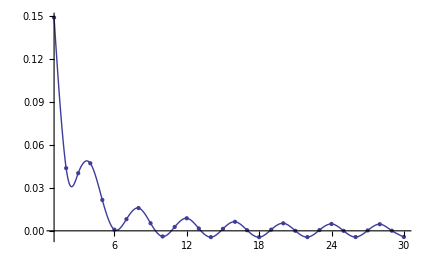

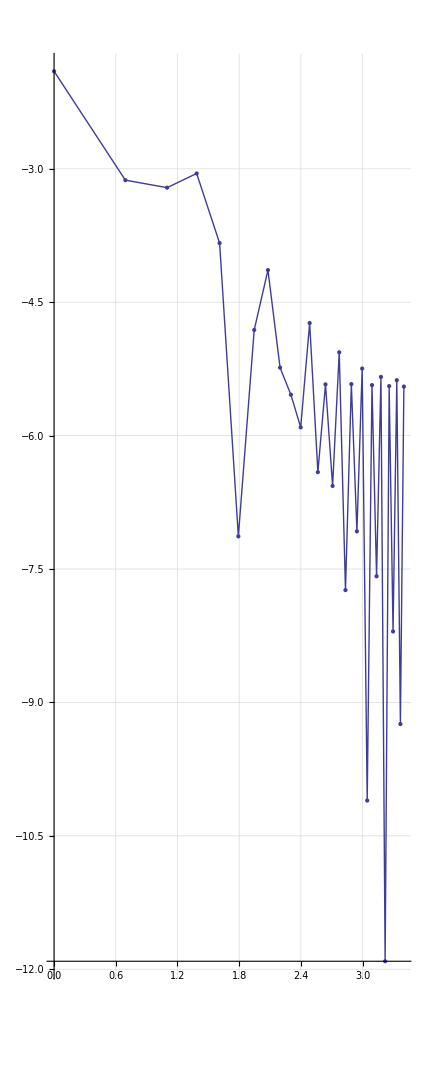

```mathematica
Module[{M,L,data},
M=TensorLoad["M"];
L=Length[M];
data=MapIndexed[{First[#2],#1}&,Re@Mean[Join[Diagonal[M,#],Diagonal[M,L-#]]]&/@Range[L/2]];
Print[Last[data]];
Print@ListLinePlot[data,PlotRange->All,InterpolationOrder->3,Mesh->Full];
ListLinePlot[{Log[#1],Log[Abs[#2]]}&@@@data,GridLines->{Range[0,4,0.1],Range[-20,7,0.1]},AspectRatio->Automatic,PlotRange->All,InterpolationOrder->1,Mesh->All]]
```

## Code

#### I/O System

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### SYSVD

```mathematica
SYSVD[A_]:=Module[{U,S,V,Θ},
{U,S,V}=SingularValueDecomposition[A];
Θ=MatrixPower[Transpose[V].U,-1/2];
{U.Θ,S,V.Θ}];
```